```mathematica
Charting`$InteractiveHighlighting=False
```

False

```mathematica
n=9; (* Number of eigenstates *)
Subscript[R, max]=3; (* Size of the box *)
δ[r_]:={r,0,Subscript[R, max]};
```

```mathematica
V[r_]:=Piecewise[{{0,Abs[r]<Subscript[R, max]},{∞,True}}];
```

```mathematica
{{μ,λ},{ϕ,ψ}}=NDEigensystem[{-1/2 Laplacian[u[r],{r}]+# u[r],DirichletCondition[u[r]==0,True]},u[r],δ[r],n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->10^-3}}}}]&/@{V[r],r^2}//Transpose;
```

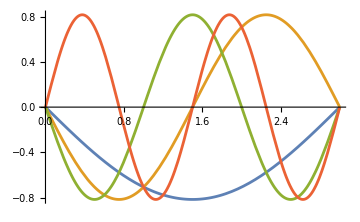
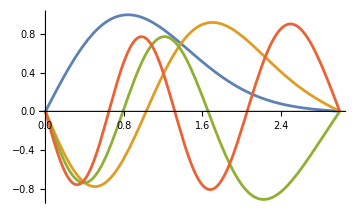

```mathematica
Plot[Take[#,4]//Evaluate,δ[r],PlotRange->All,ImageSize->Medium]&/@{ϕ,ψ}
```

```mathematica
Sort[#]&/@{μ,λ}//Column
```

{0.548311,2.19325,4.9348,8.77298,13.7078,19.7392,26.8673,35.0919,44.4132}
{2.12169,4.97382,8.07278,11.918,16.8133,22.8152,29.9239,38.1356,47.4478}

```mathematica
β=Abs[#]^2&/@ψ;
```

```mathematica
NIntegrate[#,δ[r],PrecisionGoal->4]&/@β
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
If[OddQ[n],
ν=2&/@Range[1,n-1];
AppendTo[ν,1],
ν=2&/@Range[1,n]
]
Length@ν
```

{2,2,2,2,2,2,2,2,1}

9

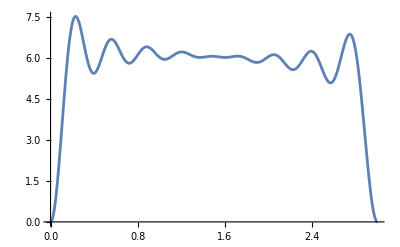

```mathematica
ρ[l_]:=ν.β/.{r->l};
Plot[ρ[r],δ[r],PlotRange->All]
```

```mathematica
Subscript[E, LDA]=-3/4(3/π)^(1/3)NIntegrate[ρ[r]^(4/3),δ[r],PrecisionGoal->4]
```

-22.7635

```mathematica
Subscript[v, LDA]=-(3/π)^(1/3)ρ[r]^(1/3);
```

```mathematica
Subscript[E, Ha]=1/2 NIntegrate[(ρ[r]ρ[l])/Abs[r-l]^2,δ[r],δ[l],PrecisionGoal->3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in r near {r,l} = {1.5,2.53237}. NIntegrate obtained 7.70662×10^8 and 1.12804×10^8 for the integral and error estimates.

3.85331×10^8

```mathematica
Subscript[v, Ha]=Integrate[ρ[l]/(√((r-l)^2+ϵ)),δ[r]];
```

```mathematica
(* Actual self-consistent loop for the Kohn-Sham equations *)
{ζ,υ}=NDEigensystem[{-1/2 Laplacian[u[r],{r}]+(Subscript[v, Ha][r]+Subscript[v, LDA]+r^2)u[r],DirichletCondition[u[r]==0,True]},u[r],δ[r],n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->10^-3}}}}];
```

$Aborted

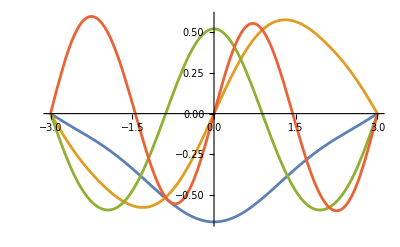

```mathematica
Plot[Take[υ,4]//Evaluate,δ[r],PlotRange->All]
```

```mathematica
Min[ζ]
```

17.3663